```mathematica
targetBase="C";
```

```mathematica
mat = MatrixPower[ConversionMatrix["E",targetBase],2];
```

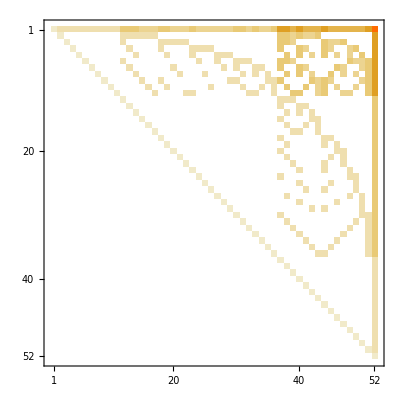

```mathematica
MatrixPlot[mat]
```

```mathematica
varsC=Bases[targetBase,"Variables"];
```

```mathematica
vars=Map[ChangeSymbol[#,"c"]&,varsC];
```

```mathematica
eqs=Table[vars[[row]]==Total[Table[mat[[row,col]]*varsC[[col]],{col,52}]],{row,52}];
```

```mathematica
repCtoM=Solve[eqs,varsC]//First;
```

```mathematica
Monitor[Table[allGraphs5[k,"colofourboega"]=Expand[allGraphs5[k,Bases[targetBase,"Colofour"]]/.repCtoM],{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
Sort[Tally[Table[Length[ListofVars[allGraphs5[k,"colofourboega"]]],{k,Keys[allGraphs5]}]]]
```

{{1,1},{2,30},{5,200},{15,640},{52,1024}}

```mathematica
Table[ShowGraph5Least[k],{k,Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourboega"]]]==1&]}]
```

{-Graphics-590481}

```mathematica
Table[ShowGraph5Least[k],{k,Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourboega"]]]==2&]}]
```

{-Graphics-298881,-Graphics-305861,-Graphics-319840,-Graphics-326841,-Graphics-361940,-Graphics-368980,-Graphics-383080,-Graphics-390141,-Graphics-492201,-Graphics-499721,-Graphics-514780,-Graphics-522321,-Graphics-560121,-Graphics-567701,-Graphics-575282,-Graphics-582881,-Graphics-544922,-Graphics-529762,-Graphics-454162,-Graphics-439081,-Graphics-408962,-Graphics-393922,-Graphics-189802,-Graphics-175681,-Graphics-147481,-Graphics-133401,-Graphics-63202,-Graphics-49201,-Graphics-21242,-Graphics-7282}

```mathematica
Table[ShowGraph5Least[k],{k,Take[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourboega"]]]==5&],5]}]
```

{-Graphics-295371,-Graphics-295600,-Graphics-296080,-Graphics-296330,-Graphics-297681}

```mathematica
allGraphs5[29537,"colofourboega"]
```

7 c12345-2 c12x345-2 c1345x2-2 c1x2345+c1x2x345